```mathematica
#OutputFunction


y1[x_] = Exp[0.05x] 
y2[x_] = Exp[0.05(x+10)]
ExpOutput = 100
```

#OutputFunction

ⅇ^(0.05 x)

ⅇ^(0.05 (10+x))

100

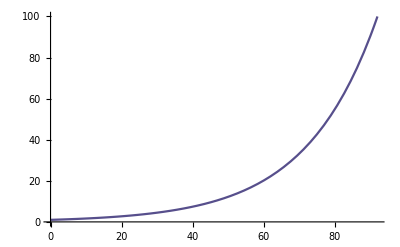

```mathematica
test = Plot[y1[x], {x, 0, 92.1034}, PlotStyle->RGBColor[0.34,0.31,0.55]]
```

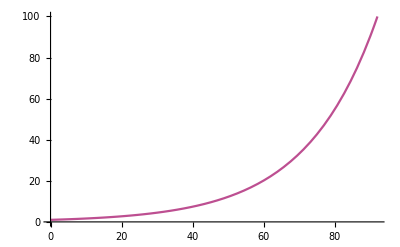

```mathematica
output1 = Plot[y1[x], {x, 0, 92.1034}, PlotStyle->RGBColor[0.74,0.31,0.57]]
```

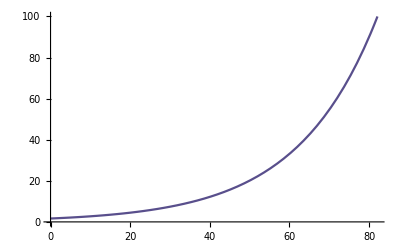

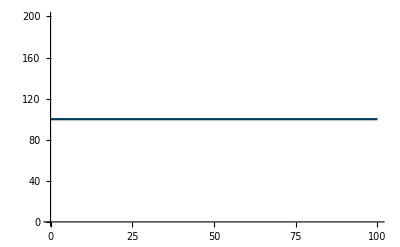

```mathematica
output2 = Plot[y2[x], {x, 0, 82.1034}, PlotStyle->RGBColor[0.35,0.31,0.55]]

expectedoutput1 = Plot[ExpOutput, {x, 0, 100}, PlotStyle->RGBColor[0, 0.24, 0.36]]
```

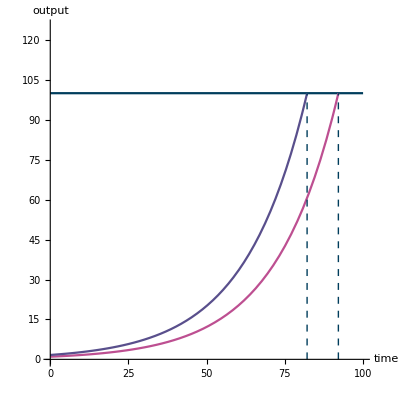

```mathematica
outputgraph1 = Show[expectedoutput1, output1, output2,Epilog->{RGBColor[0, 0.24, 0.36],Dashed, Line[{{82.1034,0},{82.1034,100}}], Line[{{92.1034,0},{92.1034,100}}]},  
AxesLabel->{time, output}, PlotRange->{{0,100},{0,125}}, AspectRatio->1]
```

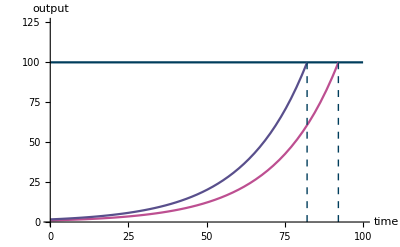
```mathematica
-Graphics-
#FigurefromToday
y3[x_] := Exp[0.05(x+92)] 
y4[x_] := Exp[0.05(x+102)]

expectedoutput2 = Plot[ExpOutput, {x, -100, 0}, PlotStyle->RGBColor[0, 0.24, 0.36]]
output3 = Plot[y3[x], {x, -100, 0}, PlotStyle->RGBColor[0.74,0.31,0.57]]
output4 = Plot[y4[x], {x, -100, -9.8966},
PlotStyle->RGBColor[0.35,0.31,0.55]]
outputgraph2 = Show[expectedoutput2, output3, output4, 
Epilog->{RGBColor[0, 0.24, 0.36],Dashed, Line[{{-9.8966,0},{-9.8966,100}}]},  
AxesLabel->{time, output},PlotRange->{{-100,0},{0,125}}]
#CompoundInterest
```

-Graphics-

#FigurefromToday

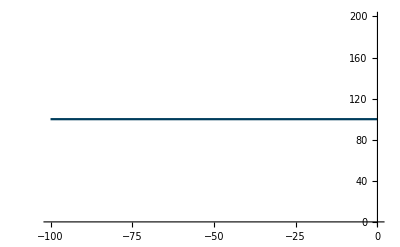

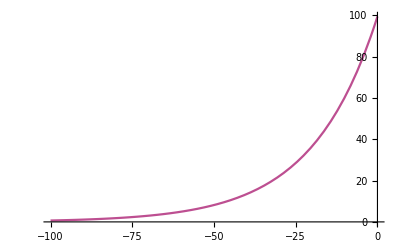

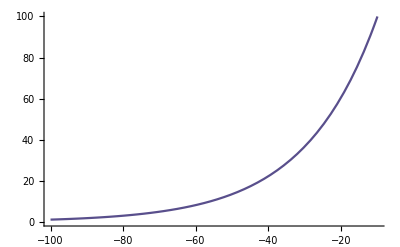

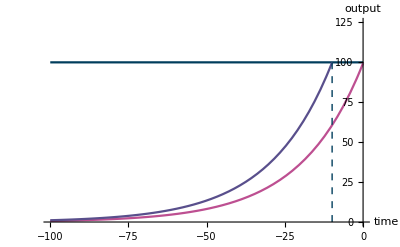

#CompoundInterest

```mathematica
#CompoundInterest
```

#CompoundInterest

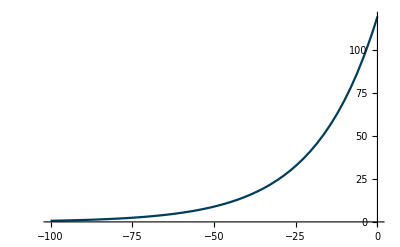

```mathematica
r3[x_] := Exp[0.052(x+92)] 

interest3 = Plot[r3[x], {x, -100, 0}, 
PlotStyle->RGBColor[0, 0.24, 0.36]]
```

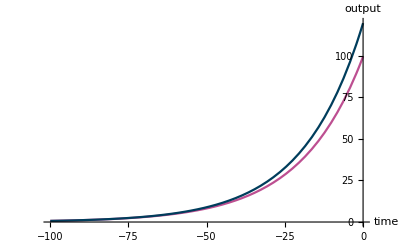

```mathematica
Show[output3, interest3,
AxesLabel->{time, output},PlotRange->{{-100,0},{0,120}}]
```